```mathematica
Clear["Global`*"];
SeedRandom[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler2`";
STEPS=3;
CHAINS=3;
```

```mathematica
SIGMA=Table[0,10,10];
For[i=1,i≤10,i++,SIGMA[[i,i]]=1/4^(2(i-1))];
U[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_]=1/2 Simplify[{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}.LinearSolve[SIGMA,{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}]];
dU[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_]=GradientG[U[x1,x2,x3,x4,x5,x6,x7,x8,x9,x10],{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}];
ddU[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_]=HessianH[U[x1,x2,x3,x4,x5,x6,x7,x8,x9,x10],{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}];
getΣ[q1_,q2_,q3_,q4_,q5_,q6_,q7_,q8_,q9_,q10_,r_]:=Module[{Σ=ddU[q1,q2,q3,q4,q5,q6,q7,q8,q9,q10],ve,e,s},
ve=Eigenvectors[Σ];
e=Eigenvalues[Σ];
s=Sign[e];
Transpose[ve].DiagonalMatrix[s Abs[e]^r].ve];
K[p1_,p2_,p3_,p4_,p5_,p6_,p7_,p8_,p9_,p10_,q1_,q2_,q3_,q4_,q5_,q6_,q7_,q8_,q9_,q10_,r_]:=Module[{Σ},
Σ=getΣ[q1,q2,q3,q4,q5,q6,q7,q8,q9,q10,r];
1/2{p1,p2,p3,p4,p5,p6,p7,p8,p9,p10}.LinearSolve[Σ,{p1,p2,p3,p4,p5,p6,p7,p8,p9,p10}]];
dKdp[p1_,p2_,p3_,p4_,p5_,p6_,p7_,p8_,p9_,p10_,q1_,q2_,q3_,q4_,q5_,q6_,q7_,q8_,q9_,q10_,r_]:=Module[{Σ},
Σ=getΣ[q1,q2,q3,q4,q5,q6,q7,q8,q9,q10,r];
LinearSolve[Σ,{p1,p2,p3,p4,p5,p6,p7,p8,p9,p10}]];
```

```mathematica
√Diagonal[SIGMA]//N
```

{1.,0.25,0.0625,0.015625,0.00390625,0.000976563,0.000244141,0.0000610352,0.0000152588,3.8147×10^-6}

```mathematica
levels=N[Table[i/2,{i,0,2}]]
```

{0.,0.5,1.}

```mathematica
QS=hmc2[U,dU,K,dKdp,10,5000,10000,{},levels];
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,16.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,256.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,4096.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,65536.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.04858×10^6,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.67772×10^7,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,2.68435×10^8,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,4.29497×10^9,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,6.87195×10^10}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

1001176712.1.444330.4421840.50635596.59122{1,2,3}{1,4}{1.11678×10^-7,0.00105115,0.00115627}{11216.1,176808.,275579.}0.00105115

200232038.115.06370.901190.1711448.833291{1,4}{1,4}{5.20987×10^-8,0.000276801,0.000368423}{35252.9,610647.,2.98557×10^6}5.20987×10^-8

30031.13376×10^70.5900160.4848740.42274822.29223{1,2}{4}{3.91425×10^-8,0.000106719,0.000251638}{35261.6,2.31889×10^6,1.13376×10^7}0.000251638

40041.30894×10^62.420420.6517440.2464222.02642{1,2}{4}{6.93433×10^-8,0.000117391,0.000117391}{12377.2,1.30897×10^6,3.91406×10^7}0.000117391

500524095.914.43650.2590620.1156749.397041{1,3}{1,4}{3.55841×10^-8,0.000117391,0.0000374043}{24105.3,3.7346×10^6,2.8965×10^8}3.55841×10^-8

60062.8965×10^85.466930.6073320.52568710.54133{1,3}{1,4}{3.55841×10^-8,0.000117391,0.0000374043}{24105.3,3.7346×10^6,2.8965×10^8}0.0000374043

70073.73459×10^62.299520.686210.49834111.84012{1,3}{1,4}{3.55841×10^-8,0.000117391,0.0000374043}{24105.3,3.7346×10^6,2.8965×10^8}0.000117391

800824090.616.54090.5642910.42035314.6671{1,3}{1,4}{3.55841×10^-8,0.000117391,0.0000374043}{24105.3,3.7346×10^6,2.8965×10^8}3.55841×10^-8

90092.8965×10^83.14020.4722990.41445916.62053{1,3}{1,4}{3.55841×10^-8,0.000117391,0.0000374043}{24105.3,3.7346×10^6,2.8965×10^8}0.0000374043

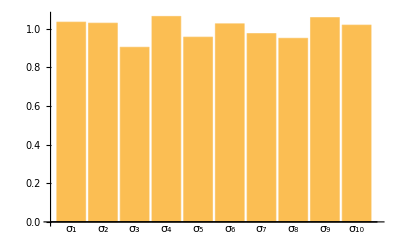

```mathematica
QS1=Table[QS[[i]],{i,1,Length[QS],CHAINS}];
QS1=QS1.MatrixPower[SIGMA,-.5];
QS2=Table[QS[[i]],{i,2,Length[QS],CHAINS}];
QS2=QS2.MatrixPower[SIGMA,-.5];
QS3=Table[QS[[i]],{i,3,Length[QS],CHAINS}];
QS3=QS3.MatrixPower[SIGMA,-.5];
BarChart[StandardDeviation[QS1],ChartLabels->{Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3],Subscript[σ, 4],Subscript[σ, 5],Subscript[σ, 6],Subscript[σ, 7],Subscript[σ, 8],Subscript[σ, 9],Subscript[σ, 10]}]
```

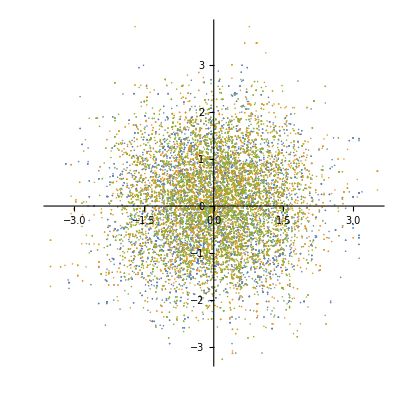

```mathematica
ListPlot[{QS1[[;;,{1,10}]],QS2[[;;,{1,10}]],QS3[[;;,{1,10}]]},AspectRatio->1]
```

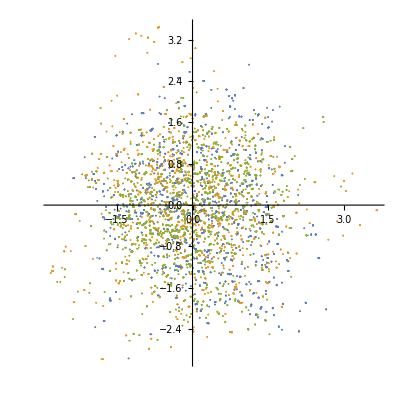

```mathematica
ListPlot[{QS1[[;;,{5,6}]],QS2[[;;,{5,6}]],QS3[[;;,{5,6}]]},AspectRatio->1]
```